# QHD for O-H Bond of the Water Molecule

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

Quantized Hamilton Dynamics (QHD) is applied to coupled Morse oscillators representing the stretching vibrations of the water molecule. QHD gives an approximation to the Heisenberg Equations of Motion (EOM). The QHD commands used in this document are included in QUANTUM, which is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce some results and graphs from Prezhdo Theor Chem Acc (2006) 116: 206-218
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2006.pdf and Prezhdo and Pereverzev in J. Chem. Phys., Vol 116, No. 11, March 2002, pages 4450-4461
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDgeneralpotential.pdf .

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Commutation Relationship

Here we define the commutation relationship that will be used in this document.
In order to enter the templates and symbols ⟦□,□⟧_-, ℏ and ⅈ you can either use the QHD palette (toolbar) or press the keys [ESC]comm[ESC], [ESC]hb[ESC] and [ESC]ii[ESC]

```mathematica
Clear[q,p];
SetQuantumObject[q,p];
⟦Subscript[q, 1],Subscript[p, 1]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 2],Subscript[p, 2]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 1],Subscript[p, 2]⟧_-=0;
⟦Subscript[q, 2],Subscript[p, 1]⟧_-=0;
⟦Subscript[q, 1],Subscript[q, 2]⟧_-=0;
⟦Subscript[p, 1],Subscript[p, 2]⟧_-=0
```

0

## Morse Potential for the O-H Bond in the Water Molecule

The potential energy that will be used in this document corresponds to two bilinearly coupled Morse oscillators, with parameter values that represent the bond stretching of the water molecule: 
V = d((1 - e^(-α q_1))^2+(1 - e^(-α q_2))^2)+k q_1 q_2  
with d=0.708 mdyn·Å, α=2.567 Å^-1, k=0.776 mdyn/Å. It is used by Prezhdo and Pereverzev in J. Chem. Phys., Vol 116, No. 11, March 2002, pages 4450-4461
 http://homepage.cem.itesm.mx/lgomez/quantum/QHDgeneralpotential.pdf .
The Morse potential is shown below, divided by the Boltzman constant, which is 0.013807 millidynes-Angstrom per KiloKelvin, in order to reproduce a figure of another paper by Prezhdo Theor Chem Acc (2006) 116: 206-218
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2006.pdf, see the graph below:

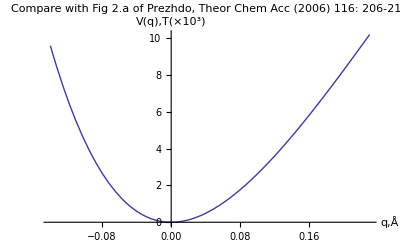

```mathematica
Plot[0.708(1-ⅇ^(-2.567q))^2/0.013807,{q,-0.14,0.23},
AxesLabel->{"q,Å","V(q),T(×10^3)"},
PlotLabel->"Compare with Fig 2.a of Prezhdo,\nTheor Chem Acc (2006) 116: 206-218"
]
```

## Fifth-order Moving-Frame Expansion of the Potential

The Morse potential energy is expanded in Taylor series around the instantaneous average value of the position variable ⟨q⟩. This is the “moving frame approximation”. A fifth order expansion is used. The resulting hamiltonian is stored in the variable hh2o below:

```mathematica
vmorse[q_]:=d(1-ⅇ^(-α q))^2;
vm5[q_]:=∑_(j=0)^5 D[ vmorse[⟨q⟩],{⟨q⟩,j} ]/(j!)(q-⟨q⟩)^j;
vh2o5=vm5[Subscript[q, 1]]+vm5[Subscript[q, 2]]+k*Subscript[q, 1]·Subscript[q, 2];
hh2o=Subscript[p, 1]^2/(2m)+Subscript[p, 2]^2/(2m)+vh2o5
```

d (1-ⅇ^(-α ⟨q_1⟩))^2+d (1-ⅇ^(-α ⟨q_2⟩))^2+p_1^2/(2 m)+p_2^2/(2 m)+2 d ⅇ^(-α ⟨q_1⟩) (1-ⅇ^(-α ⟨q_1⟩)) α (q_1-⟨q_1⟩)+1/2 d (2 ⅇ^(-2 α ⟨q_1⟩) α^2-2 ⅇ^(-α ⟨q_1⟩) (1-ⅇ^(-α ⟨q_1⟩)) α^2) (q_1-⟨q_1⟩)^2+1/6 d (-6 ⅇ^(-2 α ⟨q_1⟩) α^3+2 ⅇ^(-α ⟨q_1⟩) (1-ⅇ^(-α ⟨q_1⟩)) α^3) (q_1-⟨q_1⟩)^3+1/24 d (14 ⅇ^(-2 α ⟨q_1⟩) α^4-2 ⅇ^(-α ⟨q_1⟩) (1-ⅇ^(-α ⟨q_1⟩)) α^4) (q_1-⟨q_1⟩)^4+1/120 d (-30 ⅇ^(-2 α ⟨q_1⟩) α^5+2 ⅇ^(-α ⟨q_1⟩) (1-ⅇ^(-α ⟨q_1⟩)) α^5) (q_1-⟨q_1⟩)^5+2 d ⅇ^(-α ⟨q_2⟩) (1-ⅇ^(-α ⟨q_2⟩)) α (q_2-⟨q_2⟩)+1/2 d (2 ⅇ^(-2 α ⟨q_2⟩) α^2-2 ⅇ^(-α ⟨q_2⟩) (1-ⅇ^(-α ⟨q_2⟩)) α^2) (q_2-⟨q_2⟩)^2+1/6 d (-6 ⅇ^(-2 α ⟨q_2⟩) α^3+2 ⅇ^(-α ⟨q_2⟩) (1-ⅇ^(-α ⟨q_2⟩)) α^3) (q_2-⟨q_2⟩)^3+1/24 d (14 ⅇ^(-2 α ⟨q_2⟩) α^4-2 ⅇ^(-α ⟨q_2⟩) (1-ⅇ^(-α ⟨q_2⟩)) α^4) (q_2-⟨q_2⟩)^4+1/120 d (-30 ⅇ^(-2 α ⟨q_2⟩) α^5+2 ⅇ^(-α ⟨q_2⟩) (1-ⅇ^(-α ⟨q_2⟩)) α^5) (q_2-⟨q_2⟩)^5+k q_1·q_2

## Hierarchy of Heisenberg Equations of Motion with QHD-2 Closure

The evolution of the average of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
Consider the averages of momentum, position and their products ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩, ⟨pq⟩, ⟨p^3⟩, ⟨p^2 q⟩... The EOMs for the average values are coupled and, in general, form an infinite hierarchy of equations. Quantized Hamilton Dynamics (QHD) terminates this hierarchy by the approximation of the higher order averages via products of the lower order averages. For instance the approximation
⟨ABC⟩≈⟨AB⟩⟨C⟩+⟨AC⟩⟨B⟩+⟨BC⟩⟨A⟩-2⟨A⟩⟨B⟩⟨C⟩
can be used to approximate the third-order averages ⟨q^3⟩ and ⟨pq^2⟩_𝓈 in terms of the first and second order averages ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩ and
 ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩. 
Another further approximation is that averages of cross-term (different subindex) products are approximated by products of averages, for example:
 ⟨p_1 p_2⟩≈⟨p_1⟩⟨p_2⟩.
The command QHDHierarchy (see below) takes as its first argument the QHD order, the second argument is the variable or list of variables which are used to start the hierarchy, and the third argument is the Hamiltonian. The resulting hierarchy is stored in the variable hier and it is shown in a nice format using the command QHDForm below:

```mathematica
hier=QHDHierarchy[2,{Subscript[q, 1],Subscript[q, 2]},hh2o];
QHDForm[hier]
```

Closure procedure was applied to order 2
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨q_1⟩)/d𝓉=⟨p_1⟩/m
(d⟨q_2⟩)/d𝓉=⟨p_2⟩/m
(d⟨p_1⟩)/d𝓉=2 d ⅇ^(-2 α ⟨q_1⟩) α-2 d ⅇ^(-α ⟨q_1⟩) α-4 d ⅇ^(-2 α ⟨q_1⟩) α^3 ⟨q_1⟩^2+d ⅇ^(-α ⟨q_1⟩) α^3 ⟨q_1⟩^2+4 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨q_1⟩^4-1/4 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨q_1⟩^4+4 d ⅇ^(-2 α ⟨q_1⟩) α^3 ⟨q_1^2⟩-d ⅇ^(-α ⟨q_1⟩) α^3 ⟨q_1^2⟩-8 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨q_1⟩^2 ⟨q_1^2⟩+1/2 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨q_1⟩^2 ⟨q_1^2⟩+4 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨q_1^2⟩^2-1/4 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨q_1^2⟩^2-k ⟨q_2⟩
(d⟨p_2⟩)/d𝓉=2 d ⅇ^(-2 α ⟨q_2⟩) α-2 d ⅇ^(-α ⟨q_2⟩) α-k ⟨q_1⟩-4 d ⅇ^(-2 α ⟨q_2⟩) α^3 ⟨q_2⟩^2+d ⅇ^(-α ⟨q_2⟩) α^3 ⟨q_2⟩^2+4 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨q_2⟩^4-1/4 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨q_2⟩^4+4 d ⅇ^(-2 α ⟨q_2⟩) α^3 ⟨q_2^2⟩-d ⅇ^(-α ⟨q_2⟩) α^3 ⟨q_2^2⟩-8 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨q_2⟩^2 ⟨q_2^2⟩+1/2 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨q_2⟩^2 ⟨q_2^2⟩+4 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨q_2^2⟩^2-1/4 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨q_2^2⟩^2
(d⟨q_1^2⟩)/d𝓉=(2 ⟨p_1 q_1⟩_𝓈)/m
(d⟨q_2^2⟩)/d𝓉=(2 ⟨p_2 q_2⟩_𝓈)/m
(d⟨p_1 q_1⟩_𝓈)/d𝓉=⟨p_1^2⟩/m+2 d ⅇ^(-2 α ⟨q_1⟩) α ⟨q_1⟩-2 d ⅇ^(-α ⟨q_1⟩) α ⟨q_1⟩+4 d ⅇ^(-2 α ⟨q_1⟩) α^2 ⟨q_1⟩^2-2 d ⅇ^(-α ⟨q_1⟩) α^2 ⟨q_1⟩^2-4 d ⅇ^(-2 α ⟨q_1⟩) α^3 ⟨q_1⟩^3+d ⅇ^(-α ⟨q_1⟩) α^3 ⟨q_1⟩^3-8 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨q_1⟩^4+d ⅇ^(-α ⟨q_1⟩) α^4 ⟨q_1⟩^4+4 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨q_1⟩^5-1/4 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨q_1⟩^5-4 d ⅇ^(-2 α ⟨q_1⟩) α^2 ⟨q_1^2⟩+2 d ⅇ^(-α ⟨q_1⟩) α^2 ⟨q_1^2⟩+4 d ⅇ^(-2 α ⟨q_1⟩) α^3 ⟨q_1⟩ ⟨q_1^2⟩-d ⅇ^(-α ⟨q_1⟩) α^3 ⟨q_1⟩ ⟨q_1^2⟩+16 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨q_1⟩^2 ⟨q_1^2⟩-2 d ⅇ^(-α ⟨q_1⟩) α^4 ⟨q_1⟩^2 ⟨q_1^2⟩-8 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨q_1⟩^3 ⟨q_1^2⟩+1/2 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨q_1⟩^3 ⟨q_1^2⟩-8 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨q_1^2⟩^2+d ⅇ^(-α ⟨q_1⟩) α^4 ⟨q_1^2⟩^2+4 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨q_1⟩ ⟨q_1^2⟩^2-1/4 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨q_1⟩ ⟨q_1^2⟩^2-k ⟨q_1⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=⟨p_2^2⟩/m+2 d ⅇ^(-2 α ⟨q_2⟩) α ⟨q_2⟩-2 d ⅇ^(-α ⟨q_2⟩) α ⟨q_2⟩-k ⟨q_1⟩ ⟨q_2⟩+4 d ⅇ^(-2 α ⟨q_2⟩) α^2 ⟨q_2⟩^2-2 d ⅇ^(-α ⟨q_2⟩) α^2 ⟨q_2⟩^2-4 d ⅇ^(-2 α ⟨q_2⟩) α^3 ⟨q_2⟩^3+d ⅇ^(-α ⟨q_2⟩) α^3 ⟨q_2⟩^3-8 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨q_2⟩^4+d ⅇ^(-α ⟨q_2⟩) α^4 ⟨q_2⟩^4+4 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨q_2⟩^5-1/4 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨q_2⟩^5-4 d ⅇ^(-2 α ⟨q_2⟩) α^2 ⟨q_2^2⟩+2 d ⅇ^(-α ⟨q_2⟩) α^2 ⟨q_2^2⟩+4 d ⅇ^(-2 α ⟨q_2⟩) α^3 ⟨q_2⟩ ⟨q_2^2⟩-d ⅇ^(-α ⟨q_2⟩) α^3 ⟨q_2⟩ ⟨q_2^2⟩+16 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨q_2⟩^2 ⟨q_2^2⟩-2 d ⅇ^(-α ⟨q_2⟩) α^4 ⟨q_2⟩^2 ⟨q_2^2⟩-8 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨q_2⟩^3 ⟨q_2^2⟩+1/2 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨q_2⟩^3 ⟨q_2^2⟩-8 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨q_2^2⟩^2+d ⅇ^(-α ⟨q_2⟩) α^4 ⟨q_2^2⟩^2+4 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨q_2⟩ ⟨q_2^2⟩^2-1/4 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨q_2⟩ ⟨q_2^2⟩^2
(d⟨p_1^2⟩)/d𝓉=4 d ⅇ^(-2 α ⟨q_1⟩) α ⟨p_1⟩-4 d ⅇ^(-α ⟨q_1⟩) α ⟨p_1⟩+8 d ⅇ^(-2 α ⟨q_1⟩) α^2 ⟨p_1⟩ ⟨q_1⟩-4 d ⅇ^(-α ⟨q_1⟩) α^2 ⟨p_1⟩ ⟨q_1⟩-8 d ⅇ^(-2 α ⟨q_1⟩) α^3 ⟨p_1⟩ ⟨q_1⟩^2+2 d ⅇ^(-α ⟨q_1⟩) α^3 ⟨p_1⟩ ⟨q_1⟩^2-16 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨p_1⟩ ⟨q_1⟩^3+2 d ⅇ^(-α ⟨q_1⟩) α^4 ⟨p_1⟩ ⟨q_1⟩^3+8 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨p_1⟩ ⟨q_1⟩^4-1/2 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨p_1⟩ ⟨q_1⟩^4+8 d ⅇ^(-2 α ⟨q_1⟩) α^3 ⟨p_1⟩ ⟨q_1^2⟩-2 d ⅇ^(-α ⟨q_1⟩) α^3 ⟨p_1⟩ ⟨q_1^2⟩+16 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨p_1⟩ ⟨q_1⟩ ⟨q_1^2⟩-2 d ⅇ^(-α ⟨q_1⟩) α^4 ⟨p_1⟩ ⟨q_1⟩ ⟨q_1^2⟩-16 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨p_1⟩ ⟨q_1⟩^2 ⟨q_1^2⟩+d ⅇ^(-α ⟨q_1⟩) α^5 ⟨p_1⟩ ⟨q_1⟩^2 ⟨q_1^2⟩+8 d ⅇ^(-2 α ⟨q_1⟩) α^5 ⟨p_1⟩ ⟨q_1^2⟩^2-1/2 d ⅇ^(-α ⟨q_1⟩) α^5 ⟨p_1⟩ ⟨q_1^2⟩^2-2 k ⟨p_1⟩ ⟨q_2⟩-8 d ⅇ^(-2 α ⟨q_1⟩) α^2 ⟨p_1 q_1⟩_𝓈+4 d ⅇ^(-α ⟨q_1⟩) α^2 ⟨p_1 q_1⟩_𝓈+16 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨q_1⟩^2 ⟨p_1 q_1⟩_𝓈-2 d ⅇ^(-α ⟨q_1⟩) α^4 ⟨q_1⟩^2 ⟨p_1 q_1⟩_𝓈-16 d ⅇ^(-2 α ⟨q_1⟩) α^4 ⟨q_1^2⟩ ⟨p_1 q_1⟩_𝓈+2 d ⅇ^(-α ⟨q_1⟩) α^4 ⟨q_1^2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=4 d ⅇ^(-2 α ⟨q_2⟩) α ⟨p_2⟩-4 d ⅇ^(-α ⟨q_2⟩) α ⟨p_2⟩-2 k ⟨p_2⟩ ⟨q_1⟩+8 d ⅇ^(-2 α ⟨q_2⟩) α^2 ⟨p_2⟩ ⟨q_2⟩-4 d ⅇ^(-α ⟨q_2⟩) α^2 ⟨p_2⟩ ⟨q_2⟩-8 d ⅇ^(-2 α ⟨q_2⟩) α^3 ⟨p_2⟩ ⟨q_2⟩^2+2 d ⅇ^(-α ⟨q_2⟩) α^3 ⟨p_2⟩ ⟨q_2⟩^2-16 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨p_2⟩ ⟨q_2⟩^3+2 d ⅇ^(-α ⟨q_2⟩) α^4 ⟨p_2⟩ ⟨q_2⟩^3+8 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨p_2⟩ ⟨q_2⟩^4-1/2 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨p_2⟩ ⟨q_2⟩^4+8 d ⅇ^(-2 α ⟨q_2⟩) α^3 ⟨p_2⟩ ⟨q_2^2⟩-2 d ⅇ^(-α ⟨q_2⟩) α^3 ⟨p_2⟩ ⟨q_2^2⟩+16 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨p_2⟩ ⟨q_2⟩ ⟨q_2^2⟩-2 d ⅇ^(-α ⟨q_2⟩) α^4 ⟨p_2⟩ ⟨q_2⟩ ⟨q_2^2⟩-16 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨p_2⟩ ⟨q_2⟩^2 ⟨q_2^2⟩+d ⅇ^(-α ⟨q_2⟩) α^5 ⟨p_2⟩ ⟨q_2⟩^2 ⟨q_2^2⟩+8 d ⅇ^(-2 α ⟨q_2⟩) α^5 ⟨p_2⟩ ⟨q_2^2⟩^2-1/2 d ⅇ^(-α ⟨q_2⟩) α^5 ⟨p_2⟩ ⟨q_2^2⟩^2-8 d ⅇ^(-2 α ⟨q_2⟩) α^2 ⟨p_2 q_2⟩_𝓈+4 d ⅇ^(-α ⟨q_2⟩) α^2 ⟨p_2 q_2⟩_𝓈+16 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨q_2⟩^2 ⟨p_2 q_2⟩_𝓈-2 d ⅇ^(-α ⟨q_2⟩) α^4 ⟨q_2⟩^2 ⟨p_2 q_2⟩_𝓈-16 d ⅇ^(-2 α ⟨q_2⟩) α^4 ⟨q_2^2⟩ ⟨p_2 q_2⟩_𝓈+2 d ⅇ^(-α ⟨q_2⟩) α^4 ⟨q_2^2⟩ ⟨p_2 q_2⟩_𝓈

A hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Each arrow points from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

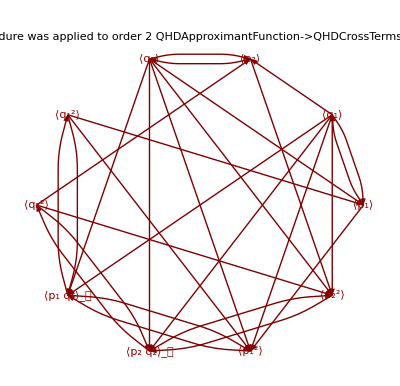

```mathematica
QHDGraphPlot[hier]
```

## Saving the Calculated Hierarchy for Future Use

The calculation of QHD hierarchies is time consuming, therefore it is a good idea to save them for future use. The simplest way to do it is using the standard Mathematica command Put. The QHD hierarchy is stored in the file HierarchyWater.m, see the command below:

```mathematica
Put[hier,"HierarchyWater.m"]
```

The command FileNames[“*.m”] can be used to see the file that was created by the command Put (together with any other preexisting file with .m extension), see the command below:

```mathematica
FileNames["*.m"]
```

{hier4.m,HierarchyWater.m,qhd2.m,qhd3.m,qhd4.m}

## Loading the Saved Hierarchy in a New Mathematica Session

Next commands have been written as they would be used in a different Mathematica session, using the command Get to load the hierarchy that was saved above (instead of calculating it again). Notice that the commutation relation and the Hamiltonian are defined again, and its important to use those that correspond to the hierarchy that is loaded. The hierarchy is shown as a graph below:

```mathematica
Needs["Quantum`QHD`"];
SetQHDAliases[];
Clear[q,p];
SetQuantumObject[q,p];
⟦Subscript[q, 1],Subscript[p, 1]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 2],Subscript[p, 2]⟧_-=ⅈ*ℏ;
⟦Subscript[q, 1],Subscript[p, 2]⟧_-=0;
⟦Subscript[q, 2],Subscript[p, 1]⟧_-=0;
⟦Subscript[q, 1],Subscript[q, 2]⟧_-=0;
⟦Subscript[p, 1],Subscript[p, 2]⟧_-=0;
vmorse[q_]:=d(1-ⅇ^(-α q))^2;
vm5[q_]:=∑_(j=0)^5 D[ vmorse[⟨q⟩],{⟨q⟩,j} ]/(j!)(q-⟨q⟩)^j;
vh2o5=vm5[Subscript[q, 1]]+vm5[Subscript[q, 2]]+k*Subscript[q, 1]·Subscript[q, 2];
hh2o=Subscript[p, 1]^2/(2m)+Subscript[p, 2]^2/(2m)+vh2o5;
hierarchy=Get["HierarchyWater.m"];
QHDGraphPlot[hierarchy]
```

-Graphics-

## Solution of the QHD Equations

Next we evaluate the hierarchy when the parameters takes the values that represent the bond stretching of the water molecule. We are using mdyn, Å and the hydrogen mass as units. The numerical version of the hierarchy is stored in the variable numhier below:

```mathematica
numhier= hierarchy/. {m->1,α->2.567,d->0.708,k->0.776 };
QHDForm[ numhier ]
```

Closure procedure was applied to order 2
QHDApproximantFunction->QHDCrossTermsApproximant. 
(d⟨q_1⟩)/d𝓉=⟨p_1⟩
(d⟨q_2⟩)/d𝓉=⟨p_2⟩
(d⟨p_1⟩)/d𝓉=3.63487 ⅇ^(-5.134 ⟨q_1⟩)-3.63487 ⅇ^(-2.567 ⟨q_1⟩)-47.9039 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^2+11.976 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^2+315.662 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^4-19.7289 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^4+47.9039 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1^2⟩-11.976 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1^2⟩-631.324 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^2 ⟨q_1^2⟩+39.4578 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^2 ⟨q_1^2⟩+315.662 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1^2⟩^2-19.7289 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1^2⟩^2-0.776 ⟨q_2⟩
(d⟨p_2⟩)/d𝓉=3.63487 ⅇ^(-5.134 ⟨q_2⟩)-3.63487 ⅇ^(-2.567 ⟨q_2⟩)-0.776 ⟨q_1⟩-47.9039 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^2+11.976 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^2+315.662 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^4-19.7289 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^4+47.9039 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2^2⟩-11.976 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2^2⟩-631.324 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^2 ⟨q_2^2⟩+39.4578 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^2 ⟨q_2^2⟩+315.662 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2^2⟩^2-19.7289 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2^2⟩^2
(d⟨q_1^2⟩)/d𝓉=2 ⟨p_1 q_1⟩_𝓈
(d⟨q_2^2⟩)/d𝓉=2 ⟨p_2 q_2⟩_𝓈
(d⟨p_1 q_1⟩_𝓈)/d𝓉=⟨p_1^2⟩+3.63487 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩-3.63487 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩+18.6614 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^2-9.33072 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^2-47.9039 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^3+11.976 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^3-245.939 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^4+30.7423 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^4+315.662 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^5-19.7289 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^5-18.6614 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1^2⟩+9.33072 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1^2⟩+47.9039 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩ ⟨q_1^2⟩-11.976 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩ ⟨q_1^2⟩+491.877 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^2 ⟨q_1^2⟩-61.4847 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^2 ⟨q_1^2⟩-631.324 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^3 ⟨q_1^2⟩+39.4578 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^3 ⟨q_1^2⟩-245.939 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1^2⟩^2+30.7423 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1^2⟩^2+315.662 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩ ⟨q_1^2⟩^2-19.7289 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩ ⟨q_1^2⟩^2-0.776 ⟨q_1⟩ ⟨q_2⟩
(d⟨p_2 q_2⟩_𝓈)/d𝓉=⟨p_2^2⟩+3.63487 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩-3.63487 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩-0.776 ⟨q_1⟩ ⟨q_2⟩+18.6614 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^2-9.33072 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^2-47.9039 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^3+11.976 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^3-245.939 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^4+30.7423 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^4+315.662 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^5-19.7289 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^5-18.6614 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2^2⟩+9.33072 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2^2⟩+47.9039 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩ ⟨q_2^2⟩-11.976 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩ ⟨q_2^2⟩+491.877 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^2 ⟨q_2^2⟩-61.4847 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^2 ⟨q_2^2⟩-631.324 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^3 ⟨q_2^2⟩+39.4578 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^3 ⟨q_2^2⟩-245.939 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2^2⟩^2+30.7423 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2^2⟩^2+315.662 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩ ⟨q_2^2⟩^2-19.7289 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩ ⟨q_2^2⟩^2
(d⟨p_1^2⟩)/d𝓉=7.26974 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩-7.26974 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩+37.3229 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩-18.6614 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩-95.8078 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^2+23.9519 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^2-491.877 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^3+61.4847 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^3+631.324 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^4-39.4578 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^4+95.8078 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1^2⟩-23.9519 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1^2⟩+491.877 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩ ⟨q_1^2⟩-61.4847 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩ ⟨q_1^2⟩-1262.65 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^2 ⟨q_1^2⟩+78.9156 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1⟩^2 ⟨q_1^2⟩+631.324 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1^2⟩^2-39.4578 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1⟩ ⟨q_1^2⟩^2-1.552 ⟨p_1⟩ ⟨q_2⟩-37.3229 ⅇ^(-5.134 ⟨q_1⟩) ⟨p_1 q_1⟩_𝓈+18.6614 ⅇ^(-2.567 ⟨q_1⟩) ⟨p_1 q_1⟩_𝓈+491.877 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1⟩^2 ⟨p_1 q_1⟩_𝓈-61.4847 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1⟩^2 ⟨p_1 q_1⟩_𝓈-491.877 ⅇ^(-5.134 ⟨q_1⟩) ⟨q_1^2⟩ ⟨p_1 q_1⟩_𝓈+61.4847 ⅇ^(-2.567 ⟨q_1⟩) ⟨q_1^2⟩ ⟨p_1 q_1⟩_𝓈
(d⟨p_2^2⟩)/d𝓉=7.26974 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩-7.26974 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩-1.552 ⟨p_2⟩ ⟨q_1⟩+37.3229 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩-18.6614 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩-95.8078 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^2+23.9519 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^2-491.877 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^3+61.4847 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^3+631.324 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^4-39.4578 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^4+95.8078 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2^2⟩-23.9519 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2^2⟩+491.877 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩ ⟨q_2^2⟩-61.4847 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩ ⟨q_2^2⟩-1262.65 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^2 ⟨q_2^2⟩+78.9156 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2⟩^2 ⟨q_2^2⟩+631.324 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2^2⟩^2-39.4578 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2⟩ ⟨q_2^2⟩^2-37.3229 ⅇ^(-5.134 ⟨q_2⟩) ⟨p_2 q_2⟩_𝓈+18.6614 ⅇ^(-2.567 ⟨q_2⟩) ⟨p_2 q_2⟩_𝓈+491.877 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2⟩^2 ⟨p_2 q_2⟩_𝓈-61.4847 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2⟩^2 ⟨p_2 q_2⟩_𝓈-491.877 ⅇ^(-5.134 ⟨q_2⟩) ⟨q_2^2⟩ ⟨p_2 q_2⟩_𝓈+61.4847 ⅇ^(-2.567 ⟨q_2⟩) ⟨q_2^2⟩ ⟨p_2 q_2⟩_𝓈

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[numhier , 0]
```

{⟨q_1⟩[0]==■,⟨q_2⟩[0]==■,⟨p_1⟩[0]==■,⟨p_2⟩[0]==■,⟨q_1^2⟩[0]==■,⟨q_2^2⟩[0]==■,⟨(p_1·q_1)_𝓈⟩[0]==■,⟨(p_2·q_2)_𝓈⟩[0]==■,⟨p_1^2⟩[0]==■,⟨p_2^2⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. Those initial values can be numbers. On the other hand, in the calculation below there are symbols like po, and then these symbols are evaluated at the desired numerical values. Notice that ℏ=0.0257772 because we are using mdyn, Å and the hydrogen mass as units. The initial conditions, which are those used by Prezhdo and Pereverzev in their paper, are stored in the variable inicond below:

```mathematica
inicond={⟨Subscript[q, 1]⟩[0]==q1o,⟨Subscript[q, 2]⟩[0]==q2o,⟨Subscript[p, 1]⟩[0]==p1o,⟨Subscript[p, 2]⟩[0]==p2o,⟨Subscript[q, 1]^2⟩[0]==q1o^2+ℏ/(2m*ω),⟨Subscript[q, 2]^2⟩[0]==q2o^2+ℏ/(2m*ω),⟨Subscript[(Subscript[p, 1]·Subscript[q, 1]), 𝓈]⟩[0]==p1o*q1o,⟨Subscript[(Subscript[p, 2]·Subscript[q, 2]), 𝓈]⟩[0]==p2o*q2o,⟨Subscript[p, 1]^2⟩[0]==p1o^2+(ℏ*m*ω)/2,⟨Subscript[p, 2]^2⟩[0]==p2o^2+(ℏ*m*ω)/2}/.
{ω->√((2 α^2*d)/m)}/.
{α->2.567,d->0.708,m->1,ℏ->0.0257772,
q1o->0,p1o->0,q2o->0.05,p2o->0}
```

{⟨q_1⟩[0]==0,⟨q_2⟩[0]==0.05,⟨p_1⟩[0]==0,⟨p_2⟩[0]==0,⟨q_1^2⟩[0]==0.00421938,⟨q_2^2⟩[0]==0.00671938,⟨(p_1·q_1)_𝓈⟩[0]==0,⟨(p_2·q_2)_𝓈⟩[0]==0.,⟨p_1^2⟩[0]==0.0393698,⟨p_2^2⟩[0]==0.0393698}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable numhier), the initial conditions (which were stored in inicond), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) expressions that depend on the dynamical variables, as it will be shown below in this document. Notice that each time unit is equal to 4.09111 femtoseconds because we are using mdyn, Å and the hydrogen mass as units, therefore in order to have a final time of 340 femtoseconds we have to use 340/4.09111as the final time. The output is stored in the variable solh2o in the calculation below:

```mathematica
solh2o=QHDNDSolve[numhier,inicond,0,340/4.09111]
```

{{⟨q_1⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨q_2⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨p_1⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨p_2⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨q_1^2⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨q_2^2⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨(p_1·q_1)_𝓈⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨(p_2·q_2)_𝓈⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨p_1^2⟩→InterpolatingFunction[{{0.,83.107}},<>],⟨p_2^2⟩→InterpolatingFunction[{{0.,83.107}},<>]}}

Next the command QHDClosure is used to obtain the QHD-2 expression for the harmonic energy of the first bond, and it is stored in the variable energy1 below:

```mathematica
energy1=QHDClosure[2,Subscript[p, 1]^2/(2m)+(m*ω^2*Subscript[q, 1]^2)/2]
```

⟨p_1^2⟩/(2 m)+1/2 m ω^2 ⟨q_1^2⟩

This is a numerical version of the QHD-2 expresson for the energy. It is stored in the variables numenergy1 below:

```mathematica
numenergy1=energy1/.{ω->√((2 α^2*d)/m)}/.{α->2.567,d->0.708,m->1}
```

⟨p_1^2⟩/2+4.66536 ⟨q_1^2⟩

QHDPlot is used to plot the QHD-2 energy for the first bond. The first argument of QHDPlot is the expression to plot, and the second argument is the numerical solution from QHDNDSolve. The energy units in the vertical axis are mdyn·Å, the time units in the horizontal axis have to be multiplied times 4.09111 in order to give femtoseconds, see the graph below:

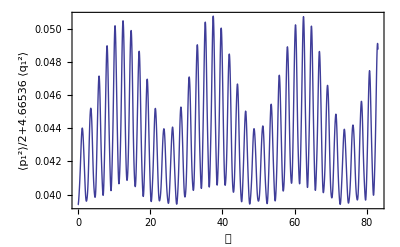

```mathematica
QHDPlot[numenergy1,solh2o]
```

The energy is multiplied by a factor of 143.926 in order to convert from mdyn·Å per molecule to kilocalories per mol, and it is plot with several formating options (QHDPlot accepts the same options as the standard Mathematica command Plot) in order to reproduce part of a figure from the paper by Prezhdo, see the graph below:

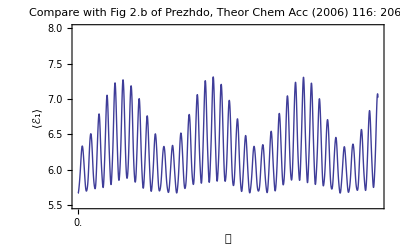

```mathematica
mytimeticks=Table[{i,4.09111*i},{i,0,500,100/4.09111}];
kcalpermol1=143.9258*numenergy1;
QHDPlot[kcalpermol1,solh2o,
FrameLabel->{𝓉,HoldForm[⟨Subscript[ℰ, 1]⟩]},
FrameTicks->{mytimeticks,Automatic,None,None},PlotStyle->Thin,
PlotRange->{5.5,8.0},
PlotLabel->"Compare with Fig 2.b of Prezhdo,\nTheor Chem Acc (2006) 116: 206-218"
]
```

This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce some of the results and graphs from  Prezhdo Theor Chem Acc (2006) 116: 206-218
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2006.pdf and Prezhdo and Pereverzev in J. Chem. Phys., Vol 116, No. 11, March 2002, pages 4450-4461
  http://homepage.cem.itesm.mx/lgomez/quantum/QHDgeneralpotential.pdf .

QUANTUM is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx